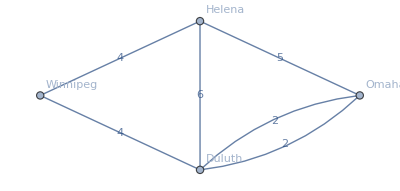

```mathematica
test = Graph[
{
"Helena"<->"Duluth",
"Helena"<->"Winnipeg",
"Winnipeg"<->"Duluth",
"Helena"<->"Omaha",
"Omaha"<->"Duluth",
"Omaha"<->"Duluth"
},
EdgeWeight->{6,4,4,5,2,2},
VertexLabels->"Name",
EdgeLabels->"EdgeWeight"]
```

```mathematica
Needs["IGraphM`"]
```

Get::noopen: Cannot open IGraphM`.

Needs::nocont: Context IGraphM` was not created when Needs was evaluated.

$Failed

```mathematica
FindShortestPath[test, "Winnipeg","Omaha"]
```

{Winnipeg,Duluth,Omaha}

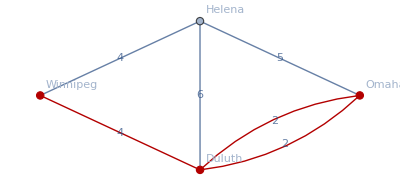

```mathematica
HighlightGraph[Graph[{"Helena", "Duluth", "Winnipeg", "Omaha"}, {UndirectedEdge["Helena", "Duluth"], UndirectedEdge["Helena", "Winnipeg"], UndirectedEdge["Winnipeg", "Duluth"], UndirectedEdge["Helena", "Omaha"], UndirectedEdge["Omaha", "Duluth"], UndirectedEdge["Omaha", "Duluth"]}, {EdgeLabels -> {"EdgeWeight"}, VertexLabels -> {"Name"}, EdgeWeight -> {6, 4, 4, 5, 2, 2}}],PathGraph[{"Winnipeg","Duluth","Omaha"}]]
```

```mathematica
AdjacencyMatrix[test]
```

SparseArray[…]

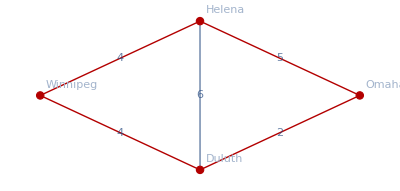

```mathematica
HighlightGraph[test,PathGraph[{"Helena", "Duluth", "Winnipeg", "Omaha"}[[%21[[2]]]]]]
```

```mathematica
test
```

-Graphics-

```mathematica
DeleteDuplicates[test, Sort]
```

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[,Sort].

DeleteDuplicates[-Graphics-,Sort]

```mathematica
WeightedAdjacencyMatrix[test]
```

SparseArray[…]

```mathematica
Grid[%38]
```

0 | 6 | 4 | 5
6 | 0 | 4 | 4
4 | 4 | 0 | 0
5 | 4 | 0 | 0

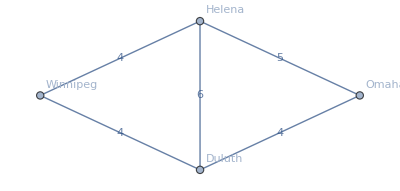

```mathematica
SimpleGraph[test]
```

```mathematica
EdgeList[test]
```

{Helena<->Duluth,Helena<->Winnipeg,Winnipeg<->Duluth,Helena<->Omaha,Omaha<->Duluth,Omaha<->Duluth}

```mathematica
PropertyValue[test, EdgeWeight]
```

{6,4,4,5,2,2}

```mathematica
Thread[{EdgeList[test], PropertyValue[test, EdgeWeight]}]
```

{{Helena<->Duluth,6},{Helena<->Winnipeg,4},{Winnipeg<->Duluth,4},{Helena<->Omaha,5},{Omaha<->Duluth,2},{Omaha<->Duluth,2}}

```mathematica
DeleteDuplicates[%]
```

{{Helena<->Duluth,6},{Helena<->Winnipeg,4},{Winnipeg<->Duluth,4},{Helena<->Omaha,5},{Omaha<->Duluth,2}}

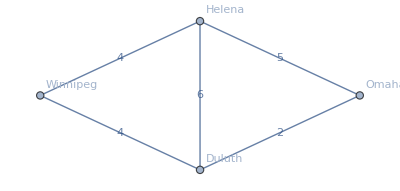

```mathematica
Graph[%48[[All,1]],EdgeWeight->%48[[All,2]],VertexLabels->"Name",
EdgeLabels->"EdgeWeight"]
```